```mathematica
(*
e[x]_here = e[1][x]_{Lagrangian approach}
*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
ass={ψ[x]∈Reals};
```

```mathematica
e[x_]:={Cos[ψ[x]],-Sin[ψ[x]]}
```

```mathematica
n[x_]:={-e[x][[2]],e[x][[1]]}/Norm[e[x]]
```

```mathematica
g[x_]:=Simplify[{{e[x].e[x]}},Assumptions->ass]
```

```mathematica
sqrtdetg[x_]:=Sqrt[Det[g[x]]]
```

```mathematica
gc[x_]:=Inverse[g[x]]
```

```mathematica
FullSimplify[{{-n'[x].e[x]}},Assumptions->ass]
```

{{-ψ'[x]}}

```mathematica
b[x_]:={{-ψ'[x]}}
```

```mathematica
1/2FullSimplify[Sum[gc[x][[i,j]]b[x][[j,i]],{i,1,1},{j,1,1}],Assumptions->ass]
```

-1/2 ψ'[x]

```mathematica
H[x_]:=-1/2 ψ'[x]
```

```mathematica
K[x_]:=0
```

```mathematica
Γ[x_]:={{{0}}}
```

```mathematica
eqψ=FullSimplify[{2 κ(2H[x](H[x]^2-K[x])+ H''[x])-2 σ[x]H[x]==0},Assumptions->ass]
```

{2 σ[x] ψ'[x]==κ (ψ'[x]^3+2 ψ^(3)[x])}

```mathematica
eqX={X1'[x]==Cos[ψ[x]],X2'[x]==-Sin[ψ[x]]}
```

{X1'[x]==Cos[ψ[x]],X2'[x]==-Sin[ψ[x]]}

```mathematica
bcs={ψ[xmin]==ψmin,ψ[xmax]==ψmax,ψ'[xmin]==ψpmin,X1[xmin]==X1min,X2[xmin]==X2min};
```

```mathematica
σ[x_]:=σc
```

```mathematica
(*parameters*)
```

```mathematica
κ=1;
σc=1;
xmin=1;
xmax=3;
ψmin=-1/2;
ψmax=25/10;
ψpmin=-1;
X1min=0;
X2min=0;
```

```mathematica
s=NDSolve[Flatten[{eqψ,eqX,bcs}],{ψ,X1,X2},{x,xmin,xmax}]
```

{{ψ→InterpolatingFunction[…],X1→InterpolatingFunction[…],X2→InterpolatingFunction[…]}}

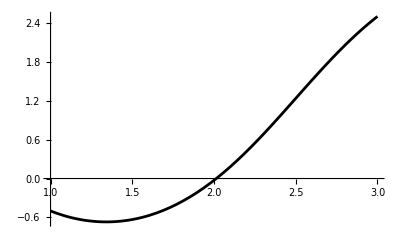

```mathematica
plotψexact=Plot[ψ[x]/.s,{x,xmin,xmax},PlotStyle->Black]
```

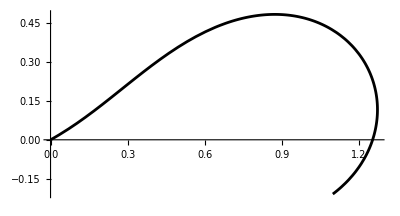

```mathematica
plotXexact=ParametricPlot[{X1[x],X2[x]}/.s,{x,xmin,xmax},PlotStyle->Black]
```

```mathematica
(*check FE solution*)
```

```mathematica
(*check ψ*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/psi.csv"];
t=Table[{t[[i,2]],t[[i,1]]},{i,2,Length[t]}]
```

{{3.,2.5},{2.9,2.28966},{2.8,2.0529},{2.7,1.79401},{2.6,1.51907},{2.5,1.23565},{2.4,0.952245},{2.3,0.677312},{2.2,0.418447},{2.1,0.181718},{2.,-0.0285883},{1.9,-0.209884},{1.8,-0.360953},{1.7,-0.481539},{1.6,-0.571934},{1.5,-0.632645},{1.4,-0.664152},{1.3,-0.666746},{1.2,-0.64045},{1.1,-0.58502},{1.,-0.5}}

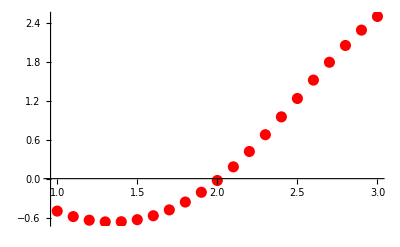

```mathematica
plotψnum=ListPlot[t,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

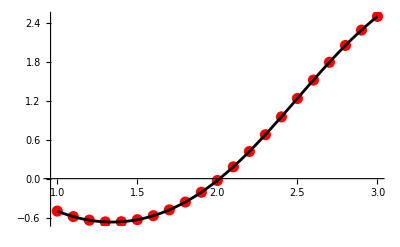

```mathematica
Show[plotψnum,plotψexact]
```

```mathematica
(*check X*)
```

```mathematica
tX=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/X.csv"];
tX=Table[{tX[[i,1]],tX[[i,2]]},{i,2,Length[tX]}]
```

{{1.09966,-0.209561},{1.17316,-0.141918},{1.2298,-0.0596734},{1.26448,0.0339404},{1.27319,0.133371},{1.2541,0.231327},{1.20832,0.320006},{1.13981,0.392599},{1.05455,0.444519},{0.959108,0.473908},{0.859499,0.481386},{0.760312,0.469324},{0.664464,0.441009},{0.573314,0.399968},{0.486976,0.349552},{0.404679,0.29276},{0.325079,0.232234},{0.24652,0.170359},{0.167235,0.10942},{0.085534,0.0517717},{0.,0.}}

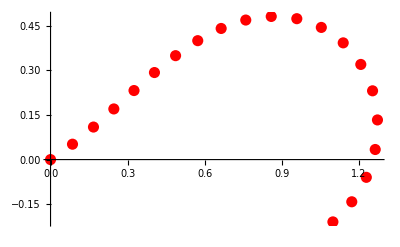

```mathematica
plotXnum=ListPlot[tX,PlotRange->Full,PlotStyle->{Red,Opacity[1],PointSize->0.02}]
```

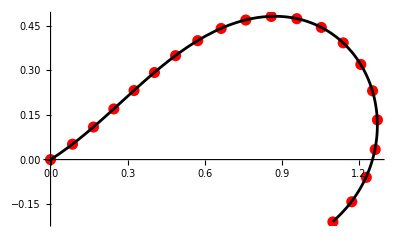

```mathematica
Show[plotXnum,plotXexact]
```

```mathematica
(*plot the normal to the manifold n*)
```

```mathematica
(*tn=Import["/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution/nodal_values/n.csv"];
tn=Table[{tn[[i,1]],tn[[i,2]]},{i,2,Length[tn]}]*)
```

```mathematica
(*plotn=Graphics[{Red,Table[Arrow[{{tX[[i,1]],tX[[i,2]]},{tX[[i,1]]+0.1*tn[[i,1]],tX[[i,2]]+0.1*tn[[i,2]]}}],{i,1,Length[t]}]},Frame->True,AspectRatio->1,PlotRange->All]*)
```